# Semi-Infinite Rod, Albedo Problem, Anisotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2015 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)
g = ‘mean cosine’ of scattering

## Analytic solutions

### Half rod reflectance/albedo (R)

```mathematica
Clear[α,g];R[α_,g_]:=(α(1-g))/(-α-α g +2 √((1-α)(1-α g))+2)
```

```mathematica
Series[R[α,g],{α,0,3}]
```

(1/4-g/4) α+(1/8-g^2/8) α^2+1/64 (5+g-g^2-5 g^3) α^3+O[α]^4

```mathematica
R[α_,g_,n_]:=α^n(SeriesCoefficient[R[A,g],{A,0,n}]/.A->α)
```

### ‘Radiance’

```mathematica
LR[x_,α_,Σt_,g_]:=ⅇ^(- Σt x √((1-α)(1-α g )))
```

```mathematica
LL[x_,α_,Σt_,g_]:=(α(1-g)E^(-Σt x √((1-α)(1-α g ))))/(-α(2 √((1-α g)/(1-α))+g+1)+2(√((1-α g)/(1-α))+1))
```

### Fluence

```mathematica
ϕ[x_,α_,Σt_,g_]:=LR[x,α,Σt,g]+LL[x,α,Σt,g]
```

### n-th collided fluence

```mathematica
ϕ[x_,α_,Σt_,g_,n_]:=α^n(SeriesCoefficient[ϕ[x,A,Σt,g],{A,0,n}]/.A->α)
```

### moments

```mathematica
ϕm[α_,Σt_,k_,g_]:=Σt^(-1-k) ((-1+α) (-1+g α))^(1/2 (-1-k)) (1+((-1+g) α)/(-2 (1+√((-1+g α)/(-1+α)))+α (1+g+2 √((-1+g α)/(-1+α))))) Gamma[1+k]
```

```mathematica
ϕm[α_,Σt_,k_,g_,n_]:=α^n(SeriesCoefficient[ϕm[A,Σt,k,g],{A,0,n}]/.A->α)
```

## load MC data

```mathematica
fs=FileNames["code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_anisotropicscatter_exp*"];
```

```mathematica
index[x_]:=Module[{data,α,Σt,g},
data=Import[x,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
g=data[[1,-1]];
{α,Σt,g,data}];
simulations=index/@fs;
```

```mathematica
alphas=Union[#[[1]]&/@simulations]
```

{0.1,0.3,0.5,0.7,0.9,0.95,0.98,0.99,0.999}

```mathematica
muts=Union[#[[2]]&/@simulations]
```

{1,3}

```mathematica
gs=Union[#[[3]]&/@simulations]
```

{-0.9,-0.7,-0.5,-0.3,-0.1,0.1,0.3,0.5,0.7,0.9}

## Monte Carlo vs Analytic

### Albedo (reflectance) variation in g

```mathematica
fsgvariation=FileNames["code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_anisotropicscatter_exp_c0.95_mut1.0_*"];
```

```mathematica
RMC[filename_]:=Module[{data},
data=Import[filename,"Table"];
{data[[1,-1]],data[[3,3]]}
]
```

```mathematica
gvariationpoints=Table[RMC[f],{f,fsgvariation}];
```

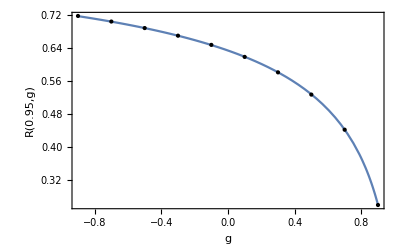

```mathematica
Clear[g];vizgvariation=Show[
Plot[R[0.95,g],{g,-0.9,0.9}],
ListPlot[gvariationpoints,PlotStyle->{PointSize[Medium],Black}],
Frame->True,FrameLabel->{{"R"[0.95,g],},{"g","Total Reflectance/Albedo R(α,g): anisotropically-scattering half rod"}}
]
```

### n-th collided albedo

```mathematica
Manipulate[
If[Length[simulations]>0,
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&][[4]];
Rs=N[{data[[5]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[R[α,g,n],{n,ns}];
j=Join[{ns},{analytic},Rs];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,alphas},{Σt,muts},{g,gs}]
```

### Internal distributions

```mathematica
Clear[alpha,Σt,g];
Manipulate[
If[Length[simulations]>0,
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&][[4]];
maxx=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];

densmom=data[[11]];

pointsCL = data[[7]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=ppoints[pointsCL,dx,maxx,Σt];
pointsCR = data[[9]];
plotpointsCR=ppoints[pointsCR,dx,maxx,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=ppoints[pointsCL+pointsCR,dx,maxx,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt,g],{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Semi-infinite rod, albedo problem, anisotropic scattering, fluence ϕ[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}}
];

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LL[x,α,Σt,g],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt,g],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Semi-infinite rod, albedo problem, anisotropic scattering, L_-[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All
];

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LR[x,α,Σt,g],{x,0,maxx},PlotRange->All],
Plot[ϕ[x,α,Σt,g],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Semi-infinite rod, albedo problem, anisotropic scattering, L_+[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All
];
Show[GraphicsGrid[{{plotϕ},{plotLL},{plotLR}}],ImageSize->500]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,alphas},{Σt,muts},{g,gs}]
```

### n-th collided radiance/angular flux

```mathematica
Manipulate[
If[Length[simulations]>0,
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&][[4]];
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

Clear[c];LnR=FullSimplify[SeriesCoefficient[LR[x,c,Σt,g],{c,0,n}] α^n];
Show[
ListPlot[ppoints[nthR[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LnR,{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{SubPlus[L]["x|"<>ToString[n]],},{x,"Semi-Infinite Rod, albedo problem, anisotropic scattering, L_+[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All,ImageSize->500
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,alphas},{Σt,muts},{g,gs},{n,Range[If[NumberQ[numcollorders],numcollorders,1]]}]
```

### N-th order Fluence / scalar flux

```mathematica
Manipulate[
If[Length[simulations]>0,
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&][[4]];
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

Show[
ListPlot[ppoints[nthR[[n+1]]+nthL[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt,g,n],{x,0,maxx},PlotRange->All]
,Frame->True,ImageSize->500,
FrameLabel->{{ϕ["x|7"],},{x,"Semi-Infinite Rod, albedo problem, anisotropic scattering, ϕ[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", g = "<>ToString[g]}},PlotRange->All
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,alphas},{Σt,muts},{g,gs},{n,Range[If[NumberQ[numcollorders],numcollorders,1]]}]
```

### Compare moments of ϕ

Divide these results, which are collision density moments, by Σt to produce radiance/fluence moments:

```mathematica
Manipulate[
If[Length[simulations]>0,
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&][[4]];
ϕmoments=N[{data[[11]]}/Σt];
ks={Table[k,{k,0,nummoments-1}]};
analytic=Table[ϕm[α,Σt,k,g],{k,ks}];
j=Join[ks,analytic,ϕmoments];
TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,alphas},{Σt,muts},{g,gs}]
```

### n-th collided moments of ϕ

```mathematica
Manipulate[
If[Length[simulations]>0,
data=SelectFirst[simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==g&][[4]];
ϕmoments=N[{data[[13+n]]}/Σt];
ks={Table[k,{k,0,nummoments-1}]};
analytic=Table[Quiet[N[ϕm[α,Σt,k,g,n]]],{k,ks}];
j=Join[ks,analytic,ϕmoments];
TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,alphas},{Σt,muts},{g,gs},{n,Range[If[NumberQ[numcollorders],numcollorders,1]]}]
```